# Exact Solution of the Younan-Veletsos Problem

Joaquin Garcia-Suarez, 2019 (All rights reserved)

This notebook details and displays the results contained in Chapter 4 section 3 and in Appendix C. Here one can find some steps of the algebra leading to the exact solution, as well as the data used to generate the plots in the body of the thesis. References to the actual text are included.

## Details on derivations

The transform of the load

It follows, for display purposes, the transform of the sign function

```mathematica
FourierTransform[2*HeavisideTheta[ξ]-1,ξ,k]
```

(ⅈ √(2/π))/k

The matrix D and the corresponding eigensystem

The matrix D appears in eq.(C.20) and its actual expression is given in (C.21):

```mathematica
Dm:={{0,c^2*k^2-r^2,ⅈ*k*(1-c^2),0},{1,0,0,0},{ⅈ*k*(1-c^2)/c^2,0,0,(k^2-r^2)/c^2},{0,0,1,0}}
```

```mathematica
Eigensystem[Dm]
```

{{-√(k^2-r^2),√(k^2-r^2),-(√(c^2 (c^2 k^2-r^2)))/c^2,(√(c^2 (c^2 k^2-r^2)))/c^2},{{(ⅈ (k^2-r^2))/k,-(ⅈ √(k^2-r^2))/k,-√(k^2-r^2),1},{(ⅈ (k^2-r^2))/k,(ⅈ √(k^2-r^2))/k,√(k^2-r^2),1},{ⅈ k,-(ⅈ k √(c^2 (c^2 k^2-r^2)))/(c^2 k^2-r^2),-(√(c^2 (c^2 k^2-r^2)))/c^2,1},{ⅈ k,(ⅈ k √(c^2 (c^2 k^2-r^2)))/(c^2 k^2-r^2),(√(c^2 (c^2 k^2-r^2)))/c^2,1}}}

Solving for the constants

Next, it follows the system of equations displayed in eq.(C.30), and the explicit solution of it, so that the reader can fathom how complex they are:

```mathematica
A=MatrixForm[{{1,1,1,1},{-(ⅈ*α)/k,(ⅈ*α)/k,-(ⅈ*k)/β,(ⅈ*k)/β},{(k+α^2/k)*Exp[-α],(k+α^2/k)*Exp[α],2*k*Exp[-β],2*k*Exp[β]},{-2α*Exp[-α],2α*Exp[α],-((c^2(β^2-k^2)+2 k^2)/β)Exp[-β],((c^2(β^2-k^2)+2 k^2)/β)Exp[β]}}]
```

(1 | 1 | 1 | 1
-(ⅈ α)/k | (ⅈ α)/k | -(ⅈ k)/β | (ⅈ k)/β
ⅇ^-α (k+α^2/k) | ⅇ^α (k+α^2/k) | 2 ⅇ^-β k | 2 ⅇ^β k
-2 ⅇ^-α α | 2 ⅇ^α α | -(ⅇ^-β (2 k^2+c^2 (-k^2+β^2)))/β | (ⅇ^β (2 k^2+c^2 (-k^2+β^2)))/β)

```mathematica
Inverse[A]
```

Inverse[(1 | 1 | 1 | 1
-(ⅈ α)/k | (ⅈ α)/k | -(ⅈ k)/β | (ⅈ k)/β
ⅇ^-α (k+α^2/k) | ⅇ^α (k+α^2/k) | 2 ⅇ^-β k | 2 ⅇ^β k
-2 ⅇ^-α α | 2 ⅇ^α α | -(ⅇ^-β (2 k^2+c^2 (-k^2+β^2)))/β | (ⅇ^β (2 k^2+c^2 (-k^2+β^2)))/β)]

```mathematica
FullSimplify[ Inverse[{{1,1,1,1},{-(ⅈ*α)/k,(ⅈ*α)/k,-(ⅈ*k)/β,(ⅈ*k)/β},{(k+α^2/k)*Exp[-α],(k+α^2/k)*Exp[α],2*k*Exp[-β],2*k*Exp[β]},{-2α*Exp[-α],2α*Exp[α],-((c^2(β^2-k^2)+2 k^2)/β)Exp[-β],((c^2(β^2-k^2)+2 k^2)/β)Exp[β]}}].{0,Sqrt[2/π] ⅈ/(k*c^2*β^2),0,-Sqrt[2/π](c^2-2)/(c^2*β^2)}]
```

{((-2+c^2) (2+ⅇ^α) (-1+ⅇ^β)^2 k^4-c^2 ⅇ^α (1+ⅇ^(2 β)) α^2 β^2+k^2 (-2 (-2+c^2) ⅇ^(α+β) α^2-2 (-2+c^2) α β+2 (-2+c^2) ⅇ^(2 β) α β+4 c^2 ⅇ^β β^2+ⅇ^α ((-2+c^2) α^2-4 α β-c^2 β^2)+ⅇ^(α+2 β) ((-2+c^2) α^2+4 α β-c^2 β^2)))/(c^2 √(2 π) β ((1+ⅇ^(2 β)) α β (-(-6+c^2) k^4-(-2+c^2) k^2 α^2+c^2 (k^2+α^2) β^2) Cosh[α]+2 ⅇ^β k^2 (-2 α β (-(-3+c^2) k^2+α^2+c^2 β^2)+((-2+c^2) k^2 (k^2+α^2)-(c^2 k^2+(4+c^2) α^2) β^2) Sinh[α] Sinh[β]))),(ⅇ^(-α-β) (-(-2+c^2) (1+2 ⅇ^α) (-1+ⅇ^β)^2 k^4+c^2 (1+ⅇ^(2 β)) α^2 β^2+k^2 (-(-2+c^2) (-1+ⅇ^β)^2 α^2+2 (2+(-2+c^2) ⅇ^α) (-1+ⅇ^(2 β)) α β+c^2 (1+ⅇ^(2 β)-4 ⅇ^(α+β)) β^2)))/(2 c^2 √(2 π) β (α β (-(-6+c^2) k^4-(-2+c^2) k^2 α^2+c^2 (k^2+α^2) β^2) Cosh[α] Cosh[β]+k^2 (-2 α β (-(-3+c^2) k^2+α^2+c^2 β^2)+((-2+c^2) k^2 (k^2+α^2)-(c^2 k^2+(4+c^2) α^2) β^2) Sinh[α] Sinh[β]))),(2 α ((1-(-2+c^2) ⅇ^β) k^2+α^2) β+α (-4 ⅇ^β k^2+(-2+c^2) (k^2+α^2)) β Cosh[α]-(k^2+α^2) ((-2+c^2) (-1+ⅇ^β) k^2-c^2 ⅇ^β β^2) Sinh[α])/(c^2 √(2 π) β (α β (-(-6+c^2) k^4-(-2+c^2) k^2 α^2+c^2 (k^2+α^2) β^2) Cosh[α] Cosh[β]+k^2 (-2 α β (-(-3+c^2) k^2+α^2+c^2 β^2)+((-2+c^2) k^2 (k^2+α^2)-(c^2 k^2+(4+c^2) α^2) β^2) Sinh[α] Sinh[β]))),(ⅇ^(-α-β) ((-2+c^2) (-1+ⅇ^(2 α)) (-1+ⅇ^β) k^4+α^2 β (c^2 (-1+ⅇ^(2 α)) β-2 ⅇ^(α+β) α (2+(-2+c^2) Cosh[α]))+k^2 ((-2+c^2) (-1+ⅇ^(2 α)) (-1+ⅇ^β) α^2+4 α β+c^2 (-1+ⅇ^(2 α)) β^2-2 ⅇ^α α β (-2 (-2+c^2+ⅇ^α)+ⅇ^β (2+(-2+c^2) Cosh[α])))))/(2 c^2 √(2 π) β (α β (-(-6+c^2) k^4-(-2+c^2) k^2 α^2+c^2 (k^2+α^2) β^2) Cosh[α] Cosh[β]+k^2 (-2 α β (-(-3+c^2) k^2+α^2+c^2 β^2)+((-2+c^2) k^2 (k^2+α^2)-(c^2 k^2+(4+c^2) α^2) β^2) Sinh[α] Sinh[β])))}

## Evaluation of the solution and plotting the results

Auxiliary Parameters

Some basic parameters that appear, over and over, in the solution: respectively, the dimensionless frequencies r and r_c (both including the damping), the dimensionless wavenumber of S waves α and of P waves β.

```mathematica
c[ν_]:=Sqrt[(2(1-ν))/(1-2ν)];
```

```mathematica
rd[r_,δ_]:=r/Sqrt[1+ⅈ*δ];
```

```mathematica
rc[r_,δ_,ν_]:=(r/c[ν])/Sqrt[1+ⅈ*δ];
```

```mathematica
α[k_,r_,δ_,ν_]:=Sqrt[k^2-rd[r,δ]^2];
```

```mathematica
β[k_,r_,δ_,ν_]:=Sqrt[k^2-rc[r,δ,ν]^2];
```

Coefficients

Express the solution of the system given in (C.30) in a way that can be easily evaluated within the notebook.

```mathematica
Ac[k_,r_,δ_,ν_]:=((-2+c[ν]^2) (2+ⅇ^α[k,r,δ,ν]) (-1+ⅇ^β[k,r,δ,ν])^2 k^4-c[ν]^2 ⅇ^α[k,r,δ,ν] (1+ⅇ^(2 β[k,r,δ,ν])) α[k,r,δ,ν]^2 β[k,r,δ,ν]^2+k^2 (-2 (-2+c[ν]^2) ⅇ^(α[k,r,δ,ν]+β[k,r,δ,ν]) α[k,r,δ,ν]^2-2 (-2+c[ν]^2) α[k,r,δ,ν] β[k,r,δ,ν]+2 (-2+c[ν]^2) ⅇ^(2 β[k,r,δ,ν]) α[k,r,δ,ν] β[k,r,δ,ν]+4 c[ν]^2 ⅇ^β[k,r,δ,ν] β[k,r,δ,ν]^2+ⅇ^α[k,r,δ,ν]((-2+c[ν]^2) α[k,r,δ,ν]^2-4 α[k,r,δ,ν] β[k,r,δ,ν]-c[ν]^2 β[k,r,δ,ν]^2)+ⅇ^(α[k,r,δ,ν]+2 β[k,r,δ,ν]) ((-2+c[ν]^2) α[k,r,δ,ν]^2+4 α[k,r,δ,ν] β[k,r,δ,ν]-c[ν]^2 β[k,r,δ,ν]^2)))/(c[ν]^2 Sqrt[2*π] β[k,r,δ,ν] ((1+ⅇ^(2 β[k,r,δ,ν]))α[k,r,δ,ν] β[k,r,δ,ν] (-(-6+c[ν]^2) k^4-(-2+c[ν]^2) k^2 α[k,r,δ,ν]^2+c[ν]^2 (k^2+α[k,r,δ,ν]^2) β[k,r,δ,ν]^2) Cosh[α[k,r,δ,ν]]+2 ⅇ^β[k,r,δ,ν] k^2 (-2 α[k,r,δ,ν] β[k,r,δ,ν] (-(-3+c[ν]^2) k^2+α[k,r,δ,ν]^2+c[ν]^2 β[k,r,δ,ν]^2)+((-2+c[ν]^2) k^2 (k^2+α[k,r,δ,ν]^2)-(c[ν]^2 k^2+(4+c[ν]^2) α[k,r,δ,ν]^2) β[k,r,δ,ν]^2) Sinh[α[k,r,δ,ν]] Sinh[β[k,r,δ,ν]])));
```

```mathematica
Bc[k_,r_,δ_,ν_]:=(ⅇ^(-α[k,r,δ,ν]-β[k,r,δ,ν]) (-(-2+c[ν]^2) (1+2 ⅇ^α[k,r,δ,ν]) (-1+ⅇ^β[k,r,δ,ν])^2 k^4+c[ν]^2 (1+ⅇ^(2 β[k,r,δ,ν])) α[k,r,δ,ν]^2 β[k,r,δ,ν]^2+k^2 (-(-2+c[ν]^2) (-1+ⅇ^β[k,r,δ,ν])^2 α[k,r,δ,ν]^2+2 (2+(-2+c[ν]^2) ⅇ^α[k,r,δ,ν]) (-1+ⅇ^(2 β[k,r,δ,ν])) α[k,r,δ,ν] β[k,r,δ,ν]+c[ν]^2 (1+ⅇ^(2 β[k,r,δ,ν])-4 ⅇ^(α[k,r,δ,ν]+β[k,r,δ,ν])) β[k,r,δ,ν]^2)))/(2 c[ν]^2 √(2 π) β[k,r,δ,ν] (α[k,r,δ,ν] β[k,r,δ,ν] (-(-6+c[ν]^2) k^4-(-2+c[ν]^2) k^2 α[k,r,δ,ν]^2+c[ν]^2 (k^2+α[k,r,δ,ν]^2) β[k,r,δ,ν]^2) Cosh[α[k,r,δ,ν]] Cosh[β[k,r,δ,ν]]+k^2 (-2 α[k,r,δ,ν] β[k,r,δ,ν] (-(-3+c[ν]^2) k^2+α[k,r,δ,ν]^2+c[ν]^2 β[k,r,δ,ν]^2)+((-2+c[ν]^2) k^2 (k^2+α[k,r,δ,ν]^2)-(c[ν]^2 k^2+(4+c[ν]^2) α[k,r,δ,ν]^2) β[k,r,δ,ν]^2) Sinh[α[k,r,δ,ν]] Sinh[β[k,r,δ,ν]])));
```

```mathematica
Cc[k_,r_,δ_,ν_]:=(2 α[k,r,δ,ν]((1-(-2+c[ν]^2) ⅇ^β[k,r,δ,ν]) k^2+α[k,r,δ,ν]^2)*β[k,r,δ,ν]+α[k,r,δ,ν] (-4 ⅇ^β[k,r,δ,ν] k^2+(-2+c[ν]^2) (k^2+α[k,r,δ,ν]^2)) β[k,r,δ,ν] Cosh[α[k,r,δ,ν]]-(k^2+α[k,r,δ,ν]^2) ((-2+c[ν]^2) (-1+ⅇ^β[k,r,δ,ν]) k^2-c[ν]^2 ⅇ^β[k,r,δ,ν] β[k,r,δ,ν]^2) Sinh[α[k,r,δ,ν]])/(c[ν]^2 Sqrt[2π] β[k,r,δ,ν] (α[k,r,δ,ν] β[k,r,δ,ν] (-(-6+c[ν]^2) k^4-(-2+c[ν]^2) k^2 α[k,r,δ,ν]^2+c[ν]^2 (k^2+α[k,r,δ,ν]^2) β[k,r,δ,ν]^2) Cosh[α[k,r,δ,ν]] Cosh[β[k,r,δ,ν]]+k^2 (-2 α[k,r,δ,ν] β[k,r,δ,ν] (-(-3+c[ν]^2) k^2+α[k,r,δ,ν]^2+c[ν]^2 β[k,r,δ,ν]^2)+((-2+c[ν]^2) k^2 (k^2+α[k,r,δ,ν]^2)-(c[ν]^2 k^2+(4+c[ν]^2) α[k,r,δ,ν]^2) β[k,r,δ,ν]^2) Sinh[α[k,r,δ,ν]] Sinh[β[k,r,δ,ν]])));
```

```mathematica
Dc[k_,r_,δ_,ν_]:=( ⅇ^(-α[k,r,δ,ν]-β[k,r,δ,ν]) ((-2+c[ν]^2) (-1+ⅇ^(2 α[k,r,δ,ν])) (-1+ⅇ^β[k,r,δ,ν]) k^4+α[k,r,δ,ν]^2 β[k,r,δ,ν] (c[ν]^2 (-1+ⅇ^(2 α[k,r,δ,ν])) β[k,r,δ,ν]-2 ⅇ^(α[k,r,δ,ν]+β[k,r,δ,ν]) α [k,r,δ,ν](2+(-2+c[ν]^2) Cosh[α[k,r,δ,ν]]))+k^2 ((-2+c[ν]^2) (-1+ⅇ^(2 α[k,r,δ,ν])) (-1+ⅇ^β[k,r,δ,ν]) α[k,r,δ,ν]^2+4 α[k,r,δ,ν] β[k,r,δ,ν]+c[ν]^2 (-1+ⅇ^(2 α[k,r,δ,ν])) β[k,r,δ,ν]^2-2 ⅇ^α[k,r,δ,ν] α[k,r,δ,ν] β[k,r,δ,ν] (-2 (-2+c[ν]^2+ⅇ^α[k,r,δ,ν])+ⅇ^β[k,r,δ,ν] (2+(-2+c[ν]^2) Cosh[α[k,r,δ,ν]])))))/(2 c[ν]^2*Sqrt[2π]* β[k,r,δ,ν] (α[k,r,δ,ν] β[k,r,δ,ν] (-(-6+c[ν]^2) k^4-(-2+c[ν]^2) k^2 α[k,r,δ,ν]^2+c[ν]^2 (k^2+α[k,r,δ,ν]^2) β[k,r,δ,ν]^2) Cosh[α[k,r,δ,ν]] Cosh[β[k,r,δ,ν]]+k^2 (-2 α[k,r,δ,ν] β[k,r,δ,ν] (-(-3+c[ν]^2) k^2+α[k,r,δ,ν]^2+c[ν]^2 β[k,r,δ,ν]^2)+((-2+c[ν]^2) k^2 (k^2+α[k,r,δ,ν]^2)-(c[ν]^2 k^2+(4+c[ν]^2) α[k,r,δ,ν]^2) β[k,r,δ,ν]^2) Sinh[α[k,r,δ,ν]] Sinh[β[k,r,δ,ν]])));
```

Variables

## Vertical displacement at the top of the wall

The vertical displacement at the top of the wall (as displayed in Figure 4.4) is expressed as an inverse transform as:

```mathematica
vtop[r_,δ_,ν_]:=2/Sqrt[2π] NIntegrate[Ac[k,r,δ,ν]*Exp[-α[k,r,δ,ν]]+Bc[k,r,δ,ν]*Exp[α[k,r,δ,ν]]+Cc[k,r,δ,ν]*Exp[-β[k,r,δ,ν]]+Dc[k,r,δ,ν]*Exp[β[k,r,δ,ν]],{k,0,10}];
```

See that this expression is just eq.(4.15) in the body of the text.

### Plots

For Figure 4.5, fix ν=0.1 and δ_d=0.16

```mathematica
NU=0.1; DE=0.16;
```

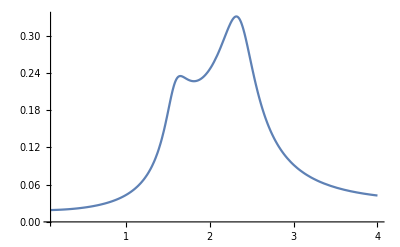

```mathematica
Plot[{Abs[vtop[r,DE,NU]]},{r,0.1,4}]
```

For Figure 4.6, fix ν=0.1 and δ_d=0.05

```mathematica
NU=0.1; DE=0.05;
```

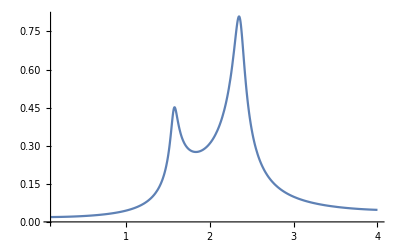

```mathematica
Plot[{Abs[vtop[r,DE,NU]]},{r,0.1,4}]
```

## Thrust

Likewise, next expression corresponds to the dimensionless thrust as in eq.(4.14):

```mathematica
Q[r_,δ_,ν_]:=1/Sqrt[2π] NIntegrate[Sqrt[2/π]/β[k,r,δ,ν]^2+Ac[k,r,δ,ν]*(c[ν]^2-2*Exp[-α[k,r,δ,ν]])+Bc[k,r,δ,ν]*(c[ν]^2-2*Exp[α[k,r,δ,ν]])+(c[ν]^2(1-(k/β[k,r,δ,ν])^2)-2)*(Cc[k,r,δ,ν]*Exp[-β[k,r,δ,ν]]+Dc[k,r,δ,ν]*Exp[β[k,r,δ,ν]])+((c[ν]*k)/β[k,r,δ,ν])^2*(Cc[k,r,δ,ν]+Dc[k,r,δ,ν]),{k,-10,10}];
```

### Plots

For Figure 4.7, fix ν=1/3 and δ_d=0.01

```mathematica
NU=1/3; DE=0.01;
```

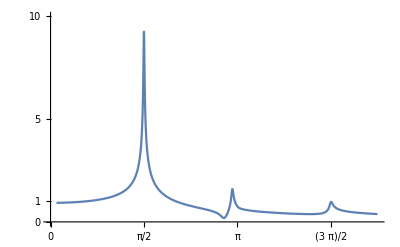

```mathematica
Plot[{Abs[Q[r,DE,NU]]},{r,0.1,3.5*π/2},PlotRange->{{0,3.5*π/2},{0,10}},Ticks->{{0,Pi/2,Pi, 3 Pi/2},{0,1,5,10}}]
```

In order to generate the results in Figure 4.8, just tweak the values if NU and DE.